## Plots Z-Prime Decay → neutrinos (Massless), M_Z'=10 TeV, C_ν_Ri^Z'≈ 1

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2  )

                          =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2 )

```mathematica
MassZprime10=10;
```

```mathematica
gVZp1=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(1))
gAZp1=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.999936

-0.0000644793

```mathematica
e^2/(sinsquared(1-sinsquared))
```

0.515835

```mathematica
Zprime10decaymassless1=MassZprime10/(12π)((gVZp1)^2+(gAZp1)^2)*10^3
```

265.224

```mathematica
Zprime10decaymassless1plot=MassZprime10/(12π)((GVZp1)^2+(GAZp1)^2)*10^3;
```

```mathematica
Plot3D[Zprime10decaymassless1plot,{GVZp1,0,1},{GAZp1,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ (GeV)"}]
```

-Graphics3D-

## Plots Z-Prime Decay → neutrinos (Massless), M_Z'=8 TeV, C_ν_Ri^Z'≈ 1

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2  )

                          =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2 )

```mathematica
MassZprime8=8;
```

```mathematica
gVZp1=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(1))
gAZp1=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.999936

-0.0000644793

```mathematica
Zprime8decaymassless1=MassZprime8/(12π)((gVZp1)^2+(gAZp1)^2)*10^3
```

212.179

```mathematica
Zprime8decaymassless1plot=MassZprime8/(12π)((GVZp1)^2+(GAZp1)^2)*10^3;
```

```mathematica
Plot3D[Zprime8decaymassless1plot,{GVZp1,0,1},{GAZp1,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ (GeV)"}]
```

-Graphics3D-

## Plots Z-Prime Decay → neutrinos (Massless), M_Z'=5 TeV, C_ν_Ri^Z'≈ 1

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2  )

                          =  (g_PQ^2 M_(Z '))/(12π) (  (1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)+2(0.1→ 1)))^2+(1/2(-1/4 e^2/(sin^2 θ_w(1-sin^2 θ_w))(0.001)))^2 )

```mathematica
MassZprime5=5;
```

```mathematica
gVZp1=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+2(1))
gAZp1=1/2(-1/4(e^2/(sinsquared(1-sinsquared)))(0.001))
```

0.999936

-0.0000644793

```mathematica
Zprime5decaymassless1=MassZprime5/(12π)((gVZp1)^2+(gAZp1)^2)*10^3
```

132.612

```mathematica
Zprime5decaymassless1plot=MassZprime5/(12π)((GVZp1)^2+(GAZp1)^2)*10^3;
```

```mathematica
Plot3D[Zprime5decaymassless1plot,{GVZp1,0,1},{GAZp1,-1,1},AxesLabel->{Subscript[g, V],Subscript[g, A],"Γ (GeV)"}]
```

-Graphics3D-

## Compare Change in Z-Prime mass

```mathematica
Zprime10decaymassless1
Zprime8decaymassless1
Zprime5decaymassless1
```

265.224

212.179

132.612

```mathematica
Zprimedecay1[Mz_]:=Mz/(12π)((gVZp1)^2+(gAZp1)^2)*10^3
```

```mathematica
Zprimedecay1[5]
Zprimedecay1[6]
Zprimedecay1[7]
Zprimedecay1[8]
Zprimedecay1[9]
Zprimedecay1[10]
Zprimedecay1[11]
Zprimedecay1[12]
```

132.612

159.134

185.657

212.179

238.702

265.224

291.746

318.269

```mathematica
DecayTable1=TableForm[{{5,Zprimedecay1[5]},{6,Zprimedecay1[6]},{7,Zprimedecay1[7]},{8,Zprimedecay1[8]},{9,Zprimedecay1[9]},{10,Zprimedecay1[10]},{11,Zprimedecay1[11]},{12,Zprimedecay1[12]}},TableHeadings-> {None,{"TeV","Decay Rate(GeV)"}}]
```

TeV | Decay Rate(GeV)
5 | 132.612
6 | 159.134
7 | 185.657
8 | 212.179
9 | 238.702
10 | 265.224
11 | 291.746
12 | 318.269

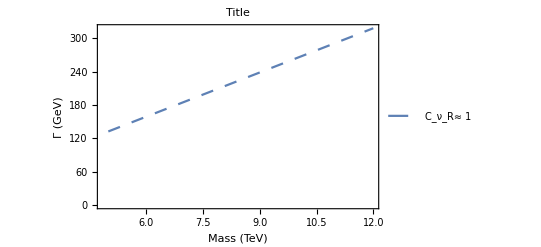

```mathematica
PlotZprimeDecay1=ListPlot[%, Joined-> True, PlotStyle->{Dashing[Medium]},PlotLegends->{" C_ν_R≈ 1"},Frame->True,FrameLabel->{"Mass (TeV)","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

## OverLay

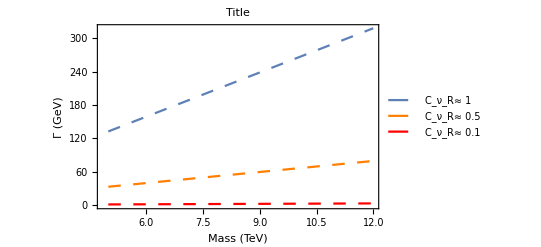

```mathematica
Show[PlotZprimeDecay1,PlotZprimeDecay05,PlotZprimeDecay01]
```

## Compare Change in C_ν_Ri^Z' with equal Z-Prime masses

```mathematica
Zprime10decaymassless01
Zprime10decaymassless05
Zprime10decaymassless1
```

2.64916

66.2975

265.224

```mathematica
Zprime8decaymassless01
Zprime8decaymassless05
Zprime8decaymassless1
```

2.11933

53.038

212.179

```mathematica
Zprime5decaymassless01
Zprime5decaymassless05
Zprime5decaymassless1
```

1.32458

33.1487

132.612

## *Note each end result is multiplied by 10^3to bring Decay Rate units in MeV